```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/richardbrower/Desktop/GitHUB_QuantumGeometry/mathematica

```mathematica
Clear[AffineTable]
```

```mathematica
(* AffineTable := Import["CutUniform48.dat"]*)
```

```mathematica
AffineTable := 
Import["../data/CutUniform48.dat"]
```

```mathematica
data := AffineTable[[All, {1,2}]]
```

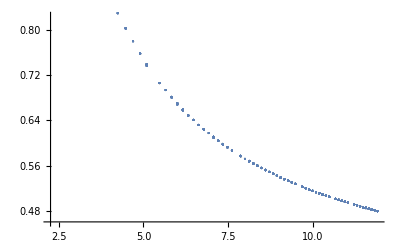

```mathematica
ListPlot[data]
```

```mathematica
(* nlmYuk=NonlinearModelFit[data,a Exp[ - b x]/x^c +d ,{a,b,c,d},x,Method->"QuasiNewton"]*)
nlmCoul=NonlinearModelFit[data,a /x^c +d ,{a,c,d},x,Method->"QuasiNewton"]
(*Method->"Newton" *)
```

FittedModel[0.298403+2.42592/x^1.04848]

```mathematica
Normal[nlmCoul]
```

0.298403+2.42592/x^1.04848

```mathematica
nlmCoul[{"BestFit","ParameterTable"}]
```

General::munfl: Exp[-12847.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12252.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-11536.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.298403+2.42592/x^1.04848, | Estimate | Standard Error | t-Statistic | P-Value
a | 2.42592 | 0.00108093 | 2244.28 | 0.
c | 1.04848 | 0.00055272 | 1896.94 | 0.
d | 0.298403 | 0.000192692 | 1548.6 | 0.}

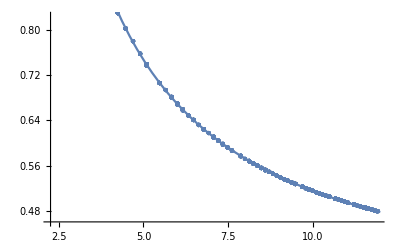

```mathematica
Show[ListPlot[data,PlotStyle->PointSize[Medium]], Plot[nlmCoul[x], {x, 1, 12}]]
```

```mathematica
nlmYuk["FitResiduals"];
nlmYuk["Properties"]
```

nlmYuk[Properties]

```mathematica
dataxyz= AffineTable[[All, {3,4,5,2}]];
```

```mathematica
r[x_,y_,z_,gyy_,gzz_, gxy_, gyz_, gzx_]:= Sqrt[x^2 + gyy  y^2 + gzz z^2 + gxy x*y   + gyz y *z  + gzx z* x];
```

```mathematica
nlmAffine=NonlinearModelFit[dataxyz, a /r[x,y,z, gyy,gzz, gxy, gyz, gzx]^c +d ,{a,c,d, {gyy,1}, {gzz,1}, { gxy,.1}, {gyz, .1}, {gzx, .1} },{x,y,z},Method->"LevenbergMarquardt"]
```

FittedModel[0.297988+2.41517/((«8»+1. z^2)^0.523616)]

```mathematica
Normal[nlmAffine]
```

0.297988+2.41517/((x^2-0.0103573 x y+1. y^2-0.0103573 x z-0.0103573 y z+1. z^2)^0.523616)

```mathematica
nlmAffine[{"BestFit","ParameterTable"}]
```

General::munfl: Exp[-12551.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-12487.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-11763.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.297988+2.41517/((x^2-0.0103573 x y+1. y^2-0.0103573 x z-0.0103573 y z+1. z^2)^0.523616), | Estimate | Standard Error | t-Statistic | P-Value
a | 2.41517 | 0.00116482 | 2073.42 | 0.
c | 1.04723 | 0.000514412 | 2035.78 | 0.
d | 0.297988 | 0.000179697 | 1658.28 | 0.
gyy | 1. | 0.000575083 | 1738.88 | 0.
gzz | 1. | 0.000575083 | 1738.88 | 0.
gxy | -0.0103573 | 0.000863042 | -12.0009 | 1.49739×10^-32
gyz | -0.0103573 | 0.000866351 | -11.9551 | 2.54719×10^-32
gzx | -0.0103573 | 0.000863042 | -12.0009 | 1.49739×10^-32}

```mathematica
nlmAffineYuk=NonlinearModelFit[dataxyz, a Exp[ - b r[x,y,z,gyy,gzz, gxy, gyz, gzx]]/r[x,y,z,gyy,gzz, gxy, gyz, gzx]^c +d ,{a,b,c,d, gyy, gzz, gxy, gyz, gzx },{x,y,z},Method->"QuasiNewton"]
```

NonlinearModelFit::nrnum: The function value 7.69698879025236×10^315+5.09131×10^33 ⅈ is not a real number at {a,b,c,d,gyy,gzz,gxy,gyz,gzx} = {10.3641,-33.5748,-11.098,-3.31048,-3.64208,-3.64208,-1.68107,-1.68107,-1.68107}.

FittedModel[0.567498+(1.00001 ⅇ^(-«19» «1»))/((x^2+«4»+«19» «1»)^0.499997)]

```mathematica
Normal[nlmAffineYuk]
```

0.567498+(1.00001 ⅇ^(-0.999999 √(x^2+0.999998 x y+1. y^2+0.999998 x z+0.999998 y z+1. z^2)))/((x^2+0.999998 x y+1. y^2+0.999998 x z+0.999998 y z+1. z^2)^0.499997)

```mathematica
nlmAffineYuk[{"BestFit","ParameterTable"}]
```

General::munfl: Exp[-5306.59] is too small to represent as a normalized machine number; precision may be lost.

{0.567498+(1.00001 ⅇ^(-0.999999 √(x^2+0.999998 x y+1. y^2+0.999998 x z+0.999998 y z+1. z^2)))/((x^2+0.999998 x y+1. y^2+0.999998 x z+0.999998 y z+1. z^2)^0.499997), | Estimate | Standard Error | t-Statistic | P-Value
a | 1.00001 | 139.511 | 0.00716795 | 0.994281
b | 0.999999 | 77.3075 | 0.0129353 | 0.98968
c | 0.999995 | 321.56 | 0.00310983 | 0.997519
d | 0.567498 | 0.00218229 | 260.047 | 0.
gyy | 1. | 4.82926 | 0.207071 | 0.835966
gzz | 1. | 4.82926 | 0.207071 | 0.835966
gxy | 0.999998 | 13.2386 | 0.0755363 | 0.939792
gyz | 0.999998 | 11.8737 | 0.0842196 | 0.932887
gzx | 0.999998 | 13.2386 | 0.0755363 | 0.939792}

```mathematica
rsqr[x_,y_,z_] = x^2+0.9999975637159478 x y+1.0000006159945258 y^2+0.9999975637159478 x z+0.9999975637159478 y z+1.0000006159945258 z^2;
Plot3D[rsqr[x,y,z], {x,-1,1},{y,-1,1}, {z,-1,1}]
```

Plot3D::nonopt: Options expected (instead of {z,-1,1}) beyond position 3 in Plot3D[rsqr[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1}]. An option must be a rule or a list of rules.

Plot3D[rsqr[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1}]

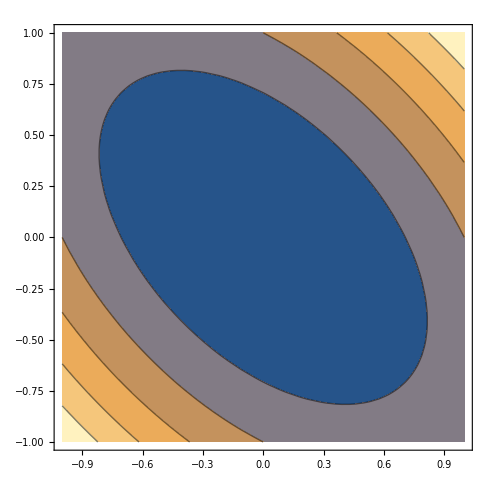

```mathematica
ContourPlot[rsqr[0,x,y],{x,-1,1},{y,-1,1}]
```